## CMT equations

```mathematica
$Assumptions={g0>0,  g0∈Reals,ωp1∈Reals,ωp2∈Reals,d1∈Reals,t∈Reals, τ∈Reals,μ∈Integers,κ[-1]∈Reals,κ[-1]>0, κ[0]∈Reals,κ[0]>0,κ[1]∈Reals,κ[1]>0,ω[-1]∈Reals,ω[-1]>0, ω[0]∈Reals,ω[0]>0,ω[1]∈Reals,ω[1]>0,  Δ∈Reals}
```

{g0>0,g0∈ℝ,ωp1∈ℝ,ωp2∈ℝ,d1∈ℝ,t∈ℝ,τ∈ℝ,μ∈ℤ,κ[-1]∈ℝ,κ[-1]>0,κ[0]∈ℝ,κ[0]>0,κ[1]∈ℝ,κ[1]>0,ω[-1]∈ℝ,ω[-1]>0,ω[0]∈ℝ,ω[0]>0,ω[1]∈ℝ,ω[1]>0,Δ∈ℝ}

```mathematica
validTriads[μ_]:=Select[Tuples[{-1,0, 1},3],(#[[1]]-#[[2]]+#[[3]]==μ)&]
(*Do[Print["μ = ",μ," → ",validTriads[μ]],{μ,{-1,0, 1}}];*)
```

```mathematica
eq[μ_]:=D[A[μ][t],t]==-(κ[μ]/2) A[μ][t]+
Sqrt[κe[μ]] Sn1*Exp[-I (ωp1-ω[μ]) t] KroneckerDelta[μ,-1]+
Sqrt[κe[μ]] S1* Exp[-I (ωp2-ω[μ]) t] KroneckerDelta[μ,1]+
I g0 Sum[With[{α=triad[[1]],β=triad[[2]],γ=triad[[3]]},
f[μ,α,β,γ]A[α][t]  Conjugate[A[β][t]] A[γ][t] Exp[-I (ω[α]-ω[β]+ω[γ]-ω[μ]) t]
],
{triad,validTriads[μ]}
];
eqsystem = Table[eq[μ],{μ,{-1,0, 1}}]
```

{A[-1]'[t]==ⅇ^(-ⅈ t (ωp1-ω[-1])) Sn1 √κe[-1]-1/2 κ[-1] A[-1][t]+ⅈ g0 (Conjugate[A[-1][t]] f[-1,-1,-1,-1] (A[-1][t])^2+Conjugate[A[0][t]] f[-1,-1,0,0] A[-1][t] A[0][t]+Conjugate[A[0][t]] f[-1,0,0,-1] A[-1][t] A[0][t]+ⅇ^(-ⅈ t (-ω[-1]+2 ω[0]-ω[1])) Conjugate[A[1][t]] f[-1,0,1,0] (A[0][t])^2+Conjugate[A[1][t]] f[-1,-1,1,1] A[-1][t] A[1][t]+Conjugate[A[1][t]] f[-1,1,1,-1] A[-1][t] A[1][t]),A[0]'[t]==-1/2 κ[0] A[0][t]+ⅈ g0 (Conjugate[A[-1][t]] f[0,-1,-1,0] A[-1][t] A[0][t]+Conjugate[A[-1][t]] f[0,0,-1,-1] A[-1][t] A[0][t]+Conjugate[A[0][t]] f[0,0,0,0] (A[0][t])^2+ⅇ^(-ⅈ t (ω[-1]-2 ω[0]+ω[1])) Conjugate[A[0][t]] f[0,-1,0,1] A[-1][t] A[1][t]+ⅇ^(-ⅈ t (ω[-1]-2 ω[0]+ω[1])) Conjugate[A[0][t]] f[0,1,0,-1] A[-1][t] A[1][t]+Conjugate[A[1][t]] f[0,0,1,1] A[0][t] A[1][t]+Conjugate[A[1][t]] f[0,1,1,0] A[0][t] A[1][t]),A[1]'[t]==ⅇ^(-ⅈ t (ωp2-ω[1])) S1 √κe[1]-1/2 κ[1] A[1][t]+ⅈ g0 (ⅇ^(-ⅈ t (-ω[-1]+2 ω[0]-ω[1])) Conjugate[A[-1][t]] f[1,0,-1,0] (A[0][t])^2+Conjugate[A[-1][t]] f[1,-1,-1,1] A[-1][t] A[1][t]+Conjugate[A[-1][t]] f[1,1,-1,-1] A[-1][t] A[1][t]+Conjugate[A[0][t]] f[1,0,0,1] A[0][t] A[1][t]+Conjugate[A[0][t]] f[1,1,0,0] A[0][t] A[1][t]+Conjugate[A[1][t]] f[1,1,1,1] (A[1][t])^2)}

```mathematica
A[μ_][t_]:=Sqrt[κ[0]/(2 g0)] a[μ][t] Exp[I (ω[μ]-ω[0]-μ*d1) t]
expr = eqsystem//Simplify;
```

```mathematica
expr = expr/. t->(2 τ)/κ[0];
```

```mathematica
rulesTime={ a[n_][(2 τ)/κ[0]]->a[n][τ],Derivative[1][a[n_]][(2 τ)/κ[0]]->(κ[0]/2) Derivative[1][a[n]][τ]};
expr= expr/.rulesTime//Simplify;
```

```mathematica
expr//MatrixForm
```

(ⅈ √2 ⅇ^((2 ⅈ τ (d1+ωp1-ω[0]))/κ[0]) √(κ[0]/g0) (-Conjugate[a[-1][τ]] f[-1,-1,-1,-1] κ[0] (a[-1][τ])^2-Conjugate[a[1][τ]] f[-1,0,1,0] κ[0] (a[0][τ])^2+a[-1][τ] (2 d1-ⅈ κ[-1]+2 ω[-1]-2 ω[0]-Conjugate[a[0][τ]] (f[-1,-1,0,0]+f[-1,0,0,-1]) κ[0] a[0][τ]-Conjugate[a[1][τ]] (f[-1,-1,1,1]+f[-1,1,1,-1]) κ[0] a[1][τ])-ⅈ κ[0] a[-1]'[τ])==4 Sn1 √κe[-1]
-ⅈ (Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+Conjugate[a[0][τ]] (f[0,-1,0,1]+f[0,1,0,-1]) a[-1][τ] a[1][τ]+a[0][τ] (ⅈ+Conjugate[a[-1][τ]] (f[0,-1,-1,0]+f[0,0,-1,-1]) a[-1][τ]+Conjugate[a[1][τ]] (f[0,0,1,1]+f[0,1,1,0]) a[1][τ])+ⅈ a[0]'[τ])==0
4 ⅇ^((2 ⅈ τ (d1-ωp2+ω[0]))/κ[0]) S1 √κe[1]+ⅈ √2 √(κ[0]/g0) (2 d1+ⅈ κ[1]+2 ω[0]-2 ω[1]+Conjugate[a[0][τ]] (f[1,0,0,1]+f[1,1,0,0]) κ[0] a[0][τ]) a[1][τ]+ⅈ √2 g0 Conjugate[a[1][τ]] f[1,1,1,1] (κ[0]/g0)^(3/2) (a[1][τ])^2+ⅈ √2 g0 Conjugate[a[-1][τ]] (κ[0]/g0)^(3/2) (f[1,0,-1,0] (a[0][τ])^2+(f[1,-1,-1,1]+f[1,1,-1,-1]) a[-1][τ] a[1][τ])==√2 g0 (κ[0]/g0)^(3/2) a[1]'[τ])

```mathematica
(*Isolando o termo da derivada*)
expr = Solve[expr,{Derivative[1][a[-1]][τ],Derivative[1][a[0]][τ],Derivative[1][a[1]][τ]}][[1]]
```

{a[-1]'[τ]→1/κ[0](-(ⅇ^(-(2 ⅈ τ (d1+ωp1-ω[0]))/κ[0]) √(g0/κ[0]) (-4 Sn1 √κe[-1]+√2 ⅇ^((2 ⅈ τ (d1+ωp1-ω[0]))/κ[0]) κ[-1] √(κ[0]/g0) a[-1][τ]))/(√2)+ⅈ (-2 d1 a[-1][τ]-2 ω[-1] a[-1][τ]+2 ω[0] a[-1][τ]+Conjugate[a[-1][τ]] f[-1,-1,-1,-1] κ[0] (a[-1][τ])^2+Conjugate[a[0][τ]] f[-1,-1,0,0] κ[0] a[-1][τ] a[0][τ]+Conjugate[a[0][τ]] f[-1,0,0,-1] κ[0] a[-1][τ] a[0][τ]+Conjugate[a[1][τ]] f[-1,0,1,0] κ[0] (a[0][τ])^2+Conjugate[a[1][τ]] f[-1,-1,1,1] κ[0] a[-1][τ] a[1][τ]+Conjugate[a[1][τ]] f[-1,1,1,-1] κ[0] a[-1][τ] a[1][τ])),a[0]'[τ]→-a[0][τ]+ⅈ (Conjugate[a[-1][τ]] f[0,-1,-1,0] a[-1][τ] a[0][τ]+Conjugate[a[-1][τ]] f[0,0,-1,-1] a[-1][τ] a[0][τ]+Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+Conjugate[a[0][τ]] f[0,-1,0,1] a[-1][τ] a[1][τ]+Conjugate[a[0][τ]] f[0,1,0,-1] a[-1][τ] a[1][τ]+Conjugate[a[1][τ]] f[0,0,1,1] a[0][τ] a[1][τ]+Conjugate[a[1][τ]] f[0,1,1,0] a[0][τ] a[1][τ]),a[1]'[τ]→1/g0(-(g0 √(g0/κ[0]) (-4 ⅇ^((2 ⅈ τ (d1-ωp2+ω[0]))/κ[0]) S1 √κe[1]+√2 √(κ[0]/g0) κ[1] a[1][τ]))/(√2 κ[0])+1/κ[0]ⅈ g0 (Conjugate[a[-1][τ]] f[1,0,-1,0] κ[0] (a[0][τ])^2+2 d1 a[1][τ]+2 ω[0] a[1][τ]-2 ω[1] a[1][τ]+Conjugate[a[-1][τ]] f[1,-1,-1,1] κ[0] a[-1][τ] a[1][τ]+Conjugate[a[-1][τ]] f[1,1,-1,-1] κ[0] a[-1][τ] a[1][τ]+Conjugate[a[0][τ]] f[1,0,0,1] κ[0] a[0][τ] a[1][τ]+Conjugate[a[0][τ]] f[1,1,0,0] κ[0] a[0][τ] a[1][τ]+Conjugate[a[1][τ]] f[1,1,1,1] κ[0] (a[1][τ])^2))}

```mathematica
rulePumps = {Sn1->s*κ[0]/Sqrt[(8*κe[-1]*g0/κ[0])], S1->s*κ[0]/Sqrt[(8*κe[1]*g0/κ[0])]};
expr = expr/.rulePumps//Simplify
```

{a[-1]'[τ]→ⅇ^(-(2 ⅈ τ (d1+ωp1-ω[0]))/κ[0]) s+ⅈ Conjugate[a[-1][τ]] f[-1,-1,-1,-1] (a[-1][τ])^2+ⅈ Conjugate[a[1][τ]] f[-1,0,1,0] (a[0][τ])^2+1/κ[0]ⅈ a[-1][τ] (-2 d1+ⅈ κ[-1]-2 ω[-1]+2 ω[0]+Conjugate[a[0][τ]] (f[-1,-1,0,0]+f[-1,0,0,-1]) κ[0] a[0][τ]+Conjugate[a[1][τ]] (f[-1,-1,1,1]+f[-1,1,1,-1]) κ[0] a[1][τ]),a[0]'[τ]→ⅈ (Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+Conjugate[a[0][τ]] (f[0,-1,0,1]+f[0,1,0,-1]) a[-1][τ] a[1][τ]+a[0][τ] (ⅈ+Conjugate[a[-1][τ]] (f[0,-1,-1,0]+f[0,0,-1,-1]) a[-1][τ]+Conjugate[a[1][τ]] (f[0,0,1,1]+f[0,1,1,0]) a[1][τ])),a[1]'[τ]→ⅇ^((2 ⅈ τ (d1-ωp2+ω[0]))/κ[0]) s+(ⅈ (2 d1+ⅈ κ[1]+2 ω[0]-2 ω[1]+Conjugate[a[0][τ]] (f[1,0,0,1]+f[1,1,0,0]) κ[0] a[0][τ]) a[1][τ])/κ[0]+ⅈ Conjugate[a[1][τ]] f[1,1,1,1] (a[1][τ])^2+ⅈ Conjugate[a[-1][τ]] (f[1,0,-1,0] (a[0][τ])^2+(f[1,-1,-1,1]+f[1,1,-1,-1]) a[-1][τ] a[1][τ])}

```mathematica
expr = expr/.{-(2*d1-2ω[0]+2ω[-1])->-(κ[0]) Δ[-1]}/.{(2d1+2ω[0]-2ω[1])->-(κ[0]) Δ[1]}//Simplify
```

{a[-1]'[τ]→ⅇ^(-(2 ⅈ τ (d1+ωp1-ω[0]))/κ[0]) s+ⅈ Conjugate[a[-1][τ]] f[-1,-1,-1,-1] (a[-1][τ])^2+ⅈ Conjugate[a[1][τ]] f[-1,0,1,0] (a[0][τ])^2+(ⅈ a[-1][τ] (ⅈ κ[-1]-Δ[-1] κ[0]+Conjugate[a[0][τ]] (f[-1,-1,0,0]+f[-1,0,0,-1]) κ[0] a[0][τ]+Conjugate[a[1][τ]] (f[-1,-1,1,1]+f[-1,1,1,-1]) κ[0] a[1][τ]))/κ[0],a[0]'[τ]→ⅈ (Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+Conjugate[a[0][τ]] (f[0,-1,0,1]+f[0,1,0,-1]) a[-1][τ] a[1][τ]+a[0][τ] (ⅈ+Conjugate[a[-1][τ]] (f[0,-1,-1,0]+f[0,0,-1,-1]) a[-1][τ]+Conjugate[a[1][τ]] (f[0,0,1,1]+f[0,1,1,0]) a[1][τ])),a[1]'[τ]→ⅇ^((2 ⅈ τ (d1-ωp2+ω[0]))/κ[0]) s+(ⅈ (-Δ[1] κ[0]+ⅈ κ[1]+Conjugate[a[0][τ]] (f[1,0,0,1]+f[1,1,0,0]) κ[0] a[0][τ]) a[1][τ])/κ[0]+ⅈ Conjugate[a[1][τ]] f[1,1,1,1] (a[1][τ])^2+ⅈ Conjugate[a[-1][τ]] (f[1,0,-1,0] (a[0][τ])^2+(f[1,-1,-1,1]+f[1,1,-1,-1]) a[-1][τ] a[1][τ])}

```mathematica
expr = expr/.{d1-ω[0]+ωp1->0}/.{d1+ω[0]-ωp2->0};
expr//MatrixForm
```

(a[-1]'[τ]→s+ⅈ Conjugate[a[-1][τ]] f[-1,-1,-1,-1] (a[-1][τ])^2+ⅈ Conjugate[a[1][τ]] f[-1,0,1,0] (a[0][τ])^2+(ⅈ a[-1][τ] (ⅈ κ[-1]-Δ[-1] κ[0]+Conjugate[a[0][τ]] (f[-1,-1,0,0]+f[-1,0,0,-1]) κ[0] a[0][τ]+Conjugate[a[1][τ]] (f[-1,-1,1,1]+f[-1,1,1,-1]) κ[0] a[1][τ]))/κ[0]
a[0]'[τ]→ⅈ (Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+Conjugate[a[0][τ]] (f[0,-1,0,1]+f[0,1,0,-1]) a[-1][τ] a[1][τ]+a[0][τ] (ⅈ+Conjugate[a[-1][τ]] (f[0,-1,-1,0]+f[0,0,-1,-1]) a[-1][τ]+Conjugate[a[1][τ]] (f[0,0,1,1]+f[0,1,1,0]) a[1][τ]))
a[1]'[τ]→s+(ⅈ (-Δ[1] κ[0]+ⅈ κ[1]+Conjugate[a[0][τ]] (f[1,0,0,1]+f[1,1,0,0]) κ[0] a[0][τ]) a[1][τ])/κ[0]+ⅈ Conjugate[a[1][τ]] f[1,1,1,1] (a[1][τ])^2+ⅈ Conjugate[a[-1][τ]] (f[1,0,-1,0] (a[0][τ])^2+(f[1,-1,-1,1]+f[1,1,-1,-1]) a[-1][τ] a[1][τ]))

```mathematica
rhs=expr[[All,2]];
rhs=rhs//Expand;
rhs//MatrixForm
```

(s-ⅈ Δ[-1] a[-1][τ]-(κ[-1] a[-1][τ])/κ[0]+ⅈ Conjugate[a[-1][τ]] f[-1,-1,-1,-1] (a[-1][τ])^2+ⅈ Conjugate[a[0][τ]] f[-1,-1,0,0] a[-1][τ] a[0][τ]+ⅈ Conjugate[a[0][τ]] f[-1,0,0,-1] a[-1][τ] a[0][τ]+ⅈ Conjugate[a[1][τ]] f[-1,0,1,0] (a[0][τ])^2+ⅈ Conjugate[a[1][τ]] f[-1,-1,1,1] a[-1][τ] a[1][τ]+ⅈ Conjugate[a[1][τ]] f[-1,1,1,-1] a[-1][τ] a[1][τ]
-a[0][τ]+ⅈ Conjugate[a[-1][τ]] f[0,-1,-1,0] a[-1][τ] a[0][τ]+ⅈ Conjugate[a[-1][τ]] f[0,0,-1,-1] a[-1][τ] a[0][τ]+ⅈ Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2+ⅈ Conjugate[a[0][τ]] f[0,-1,0,1] a[-1][τ] a[1][τ]+ⅈ Conjugate[a[0][τ]] f[0,1,0,-1] a[-1][τ] a[1][τ]+ⅈ Conjugate[a[1][τ]] f[0,0,1,1] a[0][τ] a[1][τ]+ⅈ Conjugate[a[1][τ]] f[0,1,1,0] a[0][τ] a[1][τ]
s+ⅈ Conjugate[a[-1][τ]] f[1,0,-1,0] (a[0][τ])^2-ⅈ Δ[1] a[1][τ]-(κ[1] a[1][τ])/κ[0]+ⅈ Conjugate[a[-1][τ]] f[1,-1,-1,1] a[-1][τ] a[1][τ]+ⅈ Conjugate[a[-1][τ]] f[1,1,-1,-1] a[-1][τ] a[1][τ]+ⅈ Conjugate[a[0][τ]] f[1,0,0,1] a[0][τ] a[1][τ]+ⅈ Conjugate[a[0][τ]] f[1,1,0,0] a[0][τ] a[1][τ]+ⅈ Conjugate[a[1][τ]] f[1,1,1,1] (a[1][τ])^2)

```mathematica
rhs//TeXForm
```

\left\{i f(-1,-1,-1,-1) (a(-1)(\tau ))^2 (a(-1)(\tau ))^*+i f(-1,-1,0,0) a(0)(\tau ) a(-1)(\tau ) (a(0)(\tau ))^*+i f(-1,0,0,-1) a(0)(\tau ) a(-1)(\tau ) (a(0)(\tau ))^*+i
   f(-1,-1,1,1) a(1)(\tau ) a(-1)(\tau ) (a(1)(\tau ))^*+i f(-1,1,1,-1) a(1)(\tau ) a(-1)(\tau ) (a(1)(\tau ))^*+i f(-1,0,1,0) (a(0)(\tau ))^2 (a(1)(\tau ))^*-i \Delta (-1)
   a(-1)(\tau )-\frac{\kappa (-1) a(-1)(\tau )}{\kappa (0)}+s,i f(0,0,0,0) (a(0)(\tau ))^2 (a(0)(\tau ))^*+i f(0,-1,-1,0) a(-1)(\tau ) a(0)(\tau ) (a(-1)(\tau ))^*+i
   f(0,0,-1,-1) a(-1)(\tau ) a(0)(\tau ) (a(-1)(\tau ))^*+i f(0,0,1,1) a(1)(\tau ) a(0)(\tau ) (a(1)(\tau ))^*+i f(0,1,1,0) a(1)(\tau ) a(0)(\tau ) (a(1)(\tau ))^*+i
   f(0,-1,0,1) a(-1)(\tau ) a(1)(\tau ) (a(0)(\tau ))^*+i f(0,1,0,-1) a(-1)(\tau ) a(1)(\tau ) (a(0)(\tau ))^*-a(0)(\tau ),i f(1,0,-1,0) (a(0)(\tau ))^2 (a(-1)(\tau ))^*+i
   f(1,0,0,1) a(1)(\tau ) a(0)(\tau ) (a(0)(\tau ))^*+i f(1,1,0,0) a(1)(\tau ) a(0)(\tau ) (a(0)(\tau ))^*+i f(1,1,1,1) (a(1)(\tau ))^2 (a(1)(\tau ))^*+i f(1,-1,-1,1)
   a(-1)(\tau ) a(1)(\tau ) (a(-1)(\tau ))^*+i f(1,1,-1,-1) a(-1)(\tau ) a(1)(\tau ) (a(-1)(\tau ))^*-i \Delta (1) a(1)(\tau )-\frac{\kappa (1) a(1)(\tau )}{\kappa
   (0)}+s\right\}

#### Symmetric pumps

```mathematica
rulesSymPump = {Δ[-1] ->Δp, Δ[1] ->Δp, κ[-1]->κp, κ[1]->κp , a[-1][τ]->ap[τ], a[1][τ]->ap[τ]};
rhs = rhs/.rulesSymPump;
dopoEq = rhs[[2]] - ⅈ Δ*a[0][τ];
pumpEq = rhs[[1]];
dopoEq
```

ⅈ ap[τ]^2 Conjugate[a[0][τ]] f[0,-1,0,1]+ⅈ ap[τ]^2 Conjugate[a[0][τ]] f[0,1,0,-1]-a[0][τ]-ⅈ Δ a[0][τ]+ⅈ ap[τ] Conjugate[ap[τ]] f[0,-1,-1,0] a[0][τ]+ⅈ ap[τ] Conjugate[ap[τ]] f[0,0,-1,-1] a[0][τ]+ⅈ ap[τ] Conjugate[ap[τ]] f[0,0,1,1] a[0][τ]+ⅈ ap[τ] Conjugate[ap[τ]] f[0,1,1,0] a[0][τ]+ⅈ Conjugate[a[0][τ]] f[0,0,0,0] (a[0][τ])^2

```mathematica
rulesCouplingCoefs = {f[0,1,0,-1]->f[0,-1,0,1], f[0,0,-1,-1]->f[0,-1,-1,0], f[0,0,1,1]-> f[0,1,1,0],  f[0,0,0,0]->0 };
ruleap = {ap[τ] Conjugate[ap[τ]]->P};
dopoEq = dopoEq/.rulesCouplingCoefs//Expand
(*pumpEq = pumpEq/.rulesCouplingCoefs/.{f[-1,-1,1,1]->f[-1,1,1,-1], f[-1,-1,0,0]-> f[-1,0,0,-1],f[-1,0,1,0] ->0,  f[-1,0,0,-1]->0}//Simplify;*)
```

2 ⅈ ap[τ]^2 Conjugate[a[0][τ]] f[0,-1,0,1]-a[0][τ]-ⅈ Δ a[0][τ]+2 ⅈ ap[τ] Conjugate[ap[τ]] f[0,-1,-1,0] a[0][τ]+2 ⅈ ap[τ] Conjugate[ap[τ]] f[0,1,1,0] a[0][τ]

```mathematica
Conjugate[dopoEq//Simplify]//Simplify
```

-ⅈ (-((ⅈ+Δ) Conjugate[a[0][τ]])+2 ap[τ] Conjugate[ap[τ] (f[0,-1,-1,0]+f[0,1,1,0]) a[0][τ]]+2 Conjugate[ap[τ]]^2 Conjugate[f[0,-1,0,1]] a[0][τ])

```mathematica
dopoEqConj =-ⅈ (-((ⅈ+Δ) Conjugate[a[0][τ]])+2 ap[τ] Conjugate[ap[τ]]Conjugate[ a[0][τ]] (f[0,-1,-1,0]+f[0,1,1,0])+2 Conjugate[ap[τ]]^2 f[0,-1,0,1] a[0][τ])
```

-ⅈ (-((ⅈ+Δ) Conjugate[a[0][τ]])+2 ap[τ] Conjugate[ap[τ]] Conjugate[a[0][τ]] (f[0,-1,-1,0]+f[0,1,1,0])+2 Conjugate[ap[τ]]^2 f[0,-1,0,1] a[0][τ])

#### Eigenvalue problem

```mathematica
A=Coefficient[dopoEq,a[0][τ]];
B=Coefficient[dopoEq,Conjugate[a[0][τ]]];
AConj=Coefficient[dopoEqConj,a[0][τ]];
BConj=Coefficient[dopoEqConj,Conjugate[a[0][τ]]];
```

```mathematica
M={{A,B},{AConj,BConj}};
M = M/.ap[τ] Conjugate[ap[τ]]->P//Simplify;
M//MatrixForm
```

(-1-ⅈ Δ+2 ⅈ P (f[0,-1,-1,0]+f[0,1,1,0]) | 2 ⅈ ap[τ]^2 f[0,-1,0,1]
-2 ⅈ Conjugate[ap[τ]]^2 f[0,-1,0,1] | ⅈ (ⅈ+Δ-2 P (f[0,-1,-1,0]+f[0,1,1,0])))

```mathematica
gain =Eigenvalues[M]//Simplify
```

{-1-ⅈ √(-4 ap[τ]^2 Conjugate[ap[τ]]^2 f[0,-1,0,1]^2+(Δ-2 P (f[0,-1,-1,0]+f[0,1,1,0]))^2),-1+ⅈ √(-4 ap[τ]^2 Conjugate[ap[τ]]^2 f[0,-1,0,1]^2+(Δ-2 P (f[0,-1,-1,0]+f[0,1,1,0]))^2)}

```mathematica
ruleGain = { ap[τ] Conjugate[ap[τ]]->P, ap[τ]^2 Conjugate[ap[τ]^2]->P^2, Δ - 2(f[0,-1,-1,0]+f[0,1,1,0])P->Γ};
gain =gain/.ruleGain
```

{-1-ⅈ √(Γ^2-4 P^2 f[0,-1,0,1]^2),-1+ⅈ √(Γ^2-4 P^2 f[0,-1,0,1]^2)}

```mathematica
gain = -1+ Sqrt[4 P^2 f[0,-1,0,1]^2-Γ^2]
```

-1+√(-Γ^2+4 P^2 f[0,-1,0,1]^2)

## Supermodes calculation: Assymetric molecule

```mathematica
ClearAll["Global`*"]
Ω[μ_]:=({{ω1[μ], -J12, 0}, {-J12, ω2[μ], -J23}, {0, -J23, ω3[μ]}});
```

```mathematica
ω1[μ_]:=ω0 +d1×μ+ d2/2 μ^2;
ω2[μ_]:=ω0 +D1×(2μ) + D2/2(2μ)^2;
ω3[μ_]:=ω0+d1×μ+ d2/2 μ^2;
```

```mathematica
d1 = 400;
D1 = 400/2.03;
d2 =-0.015;
D2 = -0.015;
ω0 = 0;
J12=2;
J23=2;
```

```mathematica
{vals,vecs}=Eigensystem[Ω[μ]];
pairs=Transpose[{vals,vecs}];
sortedEig[μ_]:=SortBy[pairs,First];
```

```mathematica
ωS[μ_]:=sortedEig[μ][[1,1]]
bS[μ_]:=Normalize[sortedEig[μ][[1,2]]];

ωC[μ_]:=sortedEig[μ][[2,1]];
bC[μ_]:=Normalize[sortedEig[μ][[2,2]]];

ωAS[μ_]:=sortedEig[μ][[3,1]];
bAS[μ_]:=Normalize[sortedEig[μ][[3,2]]];
```

```mathematica
(*supermode S*)
ω[1]:=ωS[μ]  
bMode[1]:=bS[μ]
(*supermode C*)
ω[2]:=ωC[μ]   
bMode[2]:=bC[μ]
(*supermode AS*)
ω[3]:=ωAS[μ]  
bMode[3]:=bAS[μ]
```

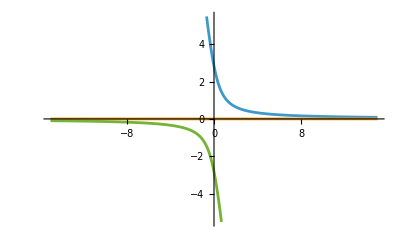

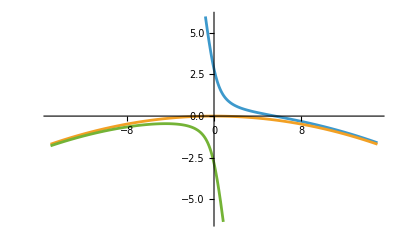

```mathematica
Plot[{ωAS[μ]-ωC[μ],ωC[μ]-ωC[μ],ωS[μ]-ωC[μ]}, {μ,-15,15}]
Plot[{ωAS[μ]-d1×μ,ωC[μ]-d1×μ,ωS[μ]-d1×μ}, {μ,-15,15}]
```

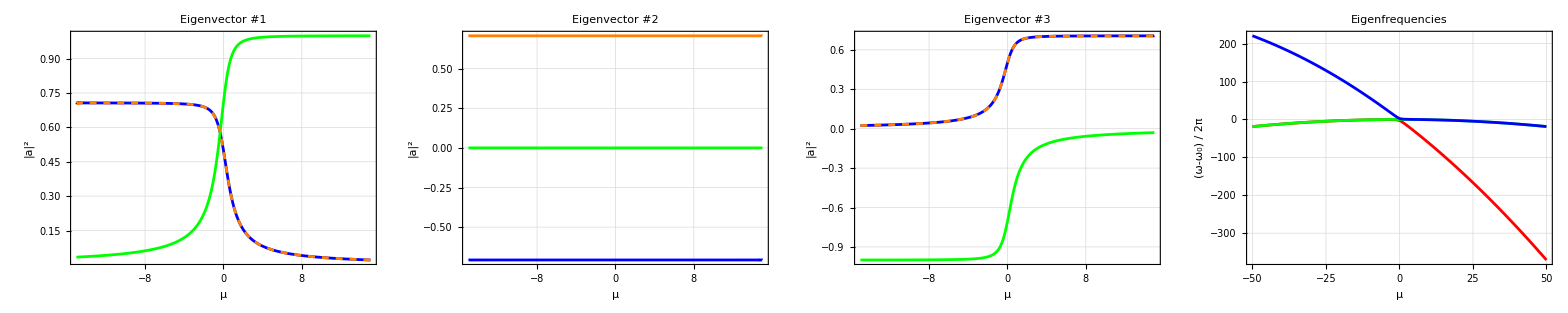

```mathematica
plt1=Plot[{bS[μ][[1]],bS[μ][[2]],bS[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #1",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Blue,Green,{Orange,Dashed}}];
plt2=Plot[{bC[μ][[1]],bC[μ][[2]],bC[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #2",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Blue,Green,Orange}];
plt3=Plot[{bAS[μ][[1]],bAS[μ][[2]],bAS[μ][[3]]},{μ,-15,15},FrameLabel->{"μ","|a|^2"},PlotLabel->"Eigenvector #3",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Blue,Green,{Orange,Dashed}}];
plt4=Plot[{ωS[μ]-d1×μ,ωC[μ]-d1×μ,ωAS[μ]-d1×μ},{μ,-50,50},FrameLabel->{"μ","(ω-ω_0) / 2π"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Red,Green,Blue}];
Grid[{{plt1,plt2,plt3,plt4}},ItemSize->Automatic,BaseStyle->ImageSizeMultipliers->1]
```

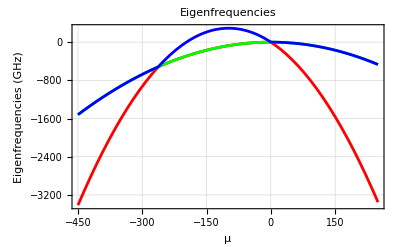

```mathematica
Plot[{ωS[μ]-d1×μ,ωC[μ]-d1×μ,ωAS[μ]-d1×μ},{μ,-450,250},FrameLabel->{"μ","Eigenfrequencies (GHz)"},PlotLabel->"Eigenfrequencies",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Red,Green,Blue}]
```

## Overlap

```mathematica
norm[μ_]:=Sum[(Conjugate[bC[μ][[i]]]bC[μ][[i]])^2,{i,1,3}] ;
norm[μ]/.μ->0
```

0.5

```mathematica
bC[μ][[3]]/.μ->0
```

0.707107

```mathematica
f[0,-1,-1,0]:=Sum[(1/(1+KroneckerDelta[2,i])Conjugate[bC[μ][[i]]] 1/(1+KroneckerDelta[2,i])bS[0][[i]])*
(1/(1+KroneckerDelta[2,i])Conjugate[bS[0][[i]]] 1/(1+KroneckerDelta[2,i])bC[μ][[i]]) ,{i,1,3}]/norm[μ]
f[0,1,1,0]:=Sum[(1/(1+KroneckerDelta[2,i])Conjugate[bC[μ][[i]]] 1/(1+KroneckerDelta[2,i])bAS[0][[i]])*
(1/(1+KroneckerDelta[2,i])Conjugate[bAS[0][[i]]] 1/(1+KroneckerDelta[2,i])bC[μ][[i]]) ,{i,1,3}]/norm[μ]

f[0,-1,0,1]:=Sum[(1/(1+KroneckerDelta[2,i])Conjugate[bC[μ][[i]]] 1/(1+KroneckerDelta[2,i])bS[0][[i]])*
(1/(1+KroneckerDelta[2,i])Conjugate[bAS[0][[i]]] 1/(1+KroneckerDelta[2,i])bC[μ][[i]]) ,{i,1,3}]/norm[μ]
```

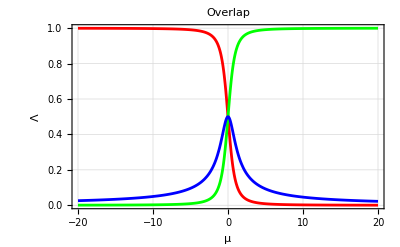

```mathematica
Plot[{f[0,-1,-1,0],f[0,1,1,0],f[0,-1,0,1]},{μ,-20,20},FrameLabel->{"μ","Λ"},PlotLabel->"Overlap",PlotRange->Full,Frame->True, GridLines->Automatic,FrameStyle->Directive[White,14],PlotStyle->{Red,Green,Blue}]
```

```mathematica
Δ=1;
P=1;
Γ:=Δ - 2(f[0,-1,-1,0]+f[0,1,1,0])P
gain := -1+ Sqrt[4 P^2 f[0,-1,0,1]^2-Γ^2]
(*DensityPlot[gain,{μ,-25,25},{P,.1,1.5}]*)
Plot[gain,{μ,-25,25}]
```

-Graphics-

## Nonlinear coupling coefficients calculation

### photonic molecule R-R-R

```mathematica
(*(* Supermodes of the 3 ring-coupled system written in the individual mode basis *)
ES[ϵ1_,ϵ2_,ϵ3_]:= 1/2 (ϵ1+√2 ϵ2+ϵ3)
EC[ϵ1_,ϵ3_]:= 1/(√2) (-ϵ1+ϵ3)
EAS[ϵ1_,ϵ2_,ϵ3_]:= 1/2 (ϵ1-√2 ϵ2+ϵ3)*)
```

```mathematica
(*(* Normalization of the nonlinear coupling coefficients by the two pumps, E1 and EAS *)
Norm1[ϵ1_,ϵ2_,ϵ3_]:=ES[ϵ1,ϵ2,ϵ3] ES[ϵ1,ϵ2,ϵ3] ES[ϵ1,ϵ2,ϵ3] ES[ϵ1,ϵ2,ϵ3]//Expand
Norm3[ϵ1_,ϵ2_,ϵ3_]:=EAS[ϵ1,ϵ2,ϵ3] EAS[ϵ1,ϵ2,ϵ3] EAS[ϵ1,ϵ2,ϵ3] EAS[ϵ1,ϵ2,ϵ3]//Expand;

NormTotal[ϵ1_,ϵ2_,ϵ3_] := Sqrt[Norm1[ϵ1,ϵ2,ϵ3] Norm3[ϵ1,ϵ2,ϵ3]]
NormTotal[ϵ1,ϵ2,ϵ3]/. Map[#^b_/;b<4->0&,{ϵ1,ϵ2,ϵ3}]/.Map[#->1&,{ϵ1,ϵ2,ϵ3}]*)
```

```mathematica
(*NormTotal [ϵ1_,ϵ2_,ϵ3_] :=(EC[ϵ1,ϵ3] Conjugate[EC[ϵ1,ϵ3]])^2;
NormTotal[ϵ1,ϵ2,ϵ3]//Expand*)
```

```mathematica
(*NormTotal [ϵ1_,ϵ2_,ϵ3_] := (( ϵ1  Conjugate[ϵ1])^4 + (ϵ3  Conjugate[ϵ3])^4)/4
NormTotal[ϵ1,ϵ2,ϵ3]//Expand*)
```

```mathematica
(*(* Nonlinear coupling coefficients *)
f111[ϵ1_,ϵ2_,ϵ3_] := ES[ϵ1,ϵ2,ϵ3] ES[ϵ1,ϵ2,ϵ3] ES[ϵ1,ϵ2,ϵ3] ES[ϵ1,ϵ2,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand
f221[ϵ1_,ϵ2_,ϵ3_] := ES[ϵ1,ϵ2,ϵ3] EC[ϵ1,ϵ3] EC[ϵ1,ϵ3] ES[ϵ1,ϵ2,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand
f331[ϵ1_,ϵ2_,ϵ3_] := ES[ϵ1,ϵ2,ϵ3] EAS[ϵ1,ϵ2,ϵ3]EAS[ϵ1,ϵ2,ϵ3] ES[ϵ1,ϵ2,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand
f232[ϵ1_,ϵ2_,ϵ3_] := ES[ϵ1,ϵ2,ϵ3] EC[ϵ1,ϵ3]EAS[ϵ1,ϵ2,ϵ3] EC[ϵ1,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand

f112[ϵ1_,ϵ2_,ϵ3_] := EC[ϵ1,ϵ3] ES[ϵ1,ϵ2,ϵ3] ES[ϵ1,ϵ2,ϵ3] EC[ϵ1,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand
f222[ϵ1_,ϵ2_,ϵ3_] := EC[ϵ1,ϵ3] EC[ϵ1,ϵ3] EC[ϵ1,ϵ3] EC[ϵ1,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand
f332[ϵ1_,ϵ2_,ϵ3_] := EC[ϵ1,ϵ3] EAS[ϵ1,ϵ2,ϵ3]EAS[ϵ1,ϵ2,ϵ3] EC[ϵ1,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand
f123[ϵ1_,ϵ2_,ϵ3_] := EC[ϵ1,ϵ3] ES[ϵ1,ϵ2,ϵ3]EC[ϵ1,ϵ3] EAS[ϵ1,ϵ2,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand

f113[ϵ1_,ϵ2_,ϵ3_] := EAS[ϵ1,ϵ2,ϵ3] ES[ϵ1,ϵ2,ϵ3] ES[ϵ1,ϵ2,ϵ3] EAS[ϵ1,ϵ2,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand
f223[ϵ1_,ϵ2_,ϵ3_] := EAS[ϵ1,ϵ2,ϵ3] EC[ϵ1,ϵ3] EC[ϵ1,ϵ3] EAS[ϵ1,ϵ2,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand
f333[ϵ1_,ϵ2_,ϵ3_] := EAS[ϵ1,ϵ2,ϵ3] EAS[ϵ1,ϵ2,ϵ3]EAS[ϵ1,ϵ2,ϵ3] EAS[ϵ1,ϵ2,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand
f212[ϵ1_,ϵ2_,ϵ3_] := EAS[ϵ1,ϵ2,ϵ3] EC[ϵ1,ϵ3]ES[ϵ1,ϵ2,ϵ3]EC[ϵ1,ϵ3]/NormTotal[ϵ1,ϵ2,ϵ3] //Expand

*)
```

```mathematica
(*Mf= {{f111[ϵ1,ϵ2,ϵ3],f221[ϵ1,ϵ2,ϵ3],f331[ϵ1,ϵ2,ϵ3],f232[ϵ1,ϵ2,ϵ3]},{f112[ϵ1,ϵ2,ϵ3],f222[ϵ1,ϵ2,ϵ3],f332[ϵ1,ϵ2,ϵ3],f123[ϵ1,ϵ2,ϵ3]},{f113[ϵ1,ϵ2,ϵ3],f223[ϵ1,ϵ2,ϵ3],f333[ϵ1,ϵ2,ϵ3],f212[ϵ1,ϵ2,ϵ3]}}/.Map[#^b_/;b<4->0&,{ϵ1,ϵ2,ϵ3}]/.Map[#->1&,{ϵ1,ϵ2,ϵ3}];

MatrixForm@{{"f111","f221","f331","f232"},{"f112","f222","f332","f123"},{"f113","f223","f333","f212"}}
MatrixForm@Mf*)
```

### Photonic molecule R-2R-R

```mathematica
(*Mf= {{f111[ϵ1,ϵ2,ϵ3],f221[ϵ1,ϵ2,ϵ3],f331[ϵ1,ϵ2,ϵ3],f232[ϵ1,ϵ2,ϵ3]},{f112[ϵ1,ϵ2,ϵ3],f222[ϵ1,ϵ2,ϵ3],f332[ϵ1,ϵ2,ϵ3],f123[ϵ1,ϵ2,ϵ3]},{f113[ϵ1,ϵ2,ϵ3],f223[ϵ1,ϵ2,ϵ3],f333[ϵ1,ϵ2,ϵ3],f212[ϵ1,ϵ2,ϵ3]}}/. Map[#^b_/;b<4->0&,{ϵ1,ϵ2,ϵ3}]/.ϵ2^4-> 1/4 ϵ2^4/.Map[#->1&,{ϵ1,ϵ2,ϵ3}];

MatrixForm@{{"f111","f221","f331","f232"},{"f112","f222","f332","f123"},{"f113","f223","f333","f212"}}
MatrixForm@Mf*)
```

```mathematica
(*rulesf = {
f[-1,-1,-1,-1]->f111[ϵ1,ϵ2,ϵ3],

f[-1,0,0,-1]->f221[ϵ1,ϵ2,ϵ3],
f[-1,-1,0,0]->f221[ϵ1,ϵ2,ϵ3],

f[-1,1,1,-1]->f331[ϵ1,ϵ2,ϵ3],
f[-1,-1,1,1]->f331[ϵ1,ϵ2,ϵ3],

f[-1,0,1,0]->f232[ϵ1,ϵ2,ϵ3],

f[0,-1,-1,0]->f112[ϵ1,ϵ2,ϵ3],
 f[0,0,-1,-1]->f112[ϵ1,ϵ2,ϵ3],

f[0,0,0,0]->f222[ϵ1,ϵ2,ϵ3],

f[0,1,1,0]->f332[ϵ1,ϵ2,ϵ3],
f[0,0,1,1]->f332[ϵ1,ϵ2,ϵ3],

f[0,-1,0,1]->f123[ϵ1,ϵ2,ϵ3],
f[0,1,0,-1]->f123[ϵ1,ϵ2,ϵ3],

f[1,-1,-1,1]->f113[ϵ1,ϵ2,ϵ3],
f[1,1,-1,-1]->f113[ϵ1,ϵ2,ϵ3],

f[1,0,0,1]->f223[ϵ1,ϵ2,ϵ3],
f[1,1,0,0]->f223[ϵ1,ϵ2,ϵ3],

f[1,1,1,1]->f333[ϵ1,ϵ2,ϵ3],
f[1,0,-1,0]->f212[ϵ1,ϵ2,ϵ3]};*)
```

```mathematica
(* rhs/.rulesf/. Map[#^b_/;b<4->0&,{ϵ1,ϵ2,ϵ3}]/.ϵ2^4-> 1/4 ϵ2^4/.Map[#->1&,{ϵ1,ϵ2,ϵ3}]//Simplify*)
```